```mathematica
description="El -> Ga El, QED, F2(0) form factor, 1-loop";
If[$FrontEnd===Null,$FeynCalcStartupMessages=False;
Print[description];];
If[$Notebooks===False,$FeynCalcStartupMessages=False];
$LoadAddOns={"FeynArts","FeynHelpers"};
<<FeynCalc`
$FAVerbose=0;
FCCheckVersion[9,3,1];
```

FeynCalc 10.1.0 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.12 (24 May 2024) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FeynHelpers 2.0.0 (). For help, use the online documentation, visit the forum and have a look at the supplied examples.The PDF-version of the manual can be downloaded here.

If you use FeynHelpers in your research, please evaluate FeynHelpersHowToCite[] to learn how to cite this work.

## Generate all desired 1-Loop diagrams using FeynArts

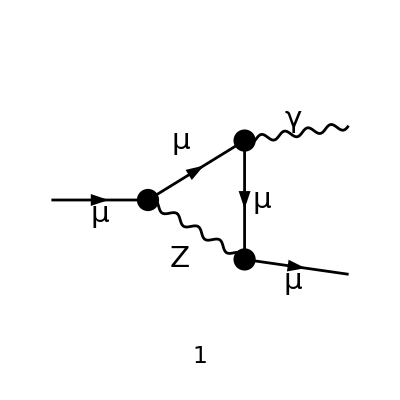

```mathematica
MakeBoxes[mu,TraditionalForm]:="μ";
MakeBoxes[p1,TraditionalForm]:="\!\(\*SubscriptBox[\(p\), \(1\)]\)";
MakeBoxes[p2,TraditionalForm]:="\!\(\*SubscriptBox[\(p\), \(2\)]\)";
diags=InsertFields[CreateTopologies[1,1->2,ExcludeTopologies->{Tadpoles,WFCorrections}],{F[2,{2}]}->{V[1],F[2,{2}]},InsertionLevel->{Classes},ExcludeParticles->{S[1],S[3],V[1],V[3]}];
(*diagsCT=InsertFields[CreateCTTopologies[1,1->2,ExcludeTopologies->{Tadpoles,WFCorrections}],{F[2,{1}]}->{V[1],F[2,{1}]},InsertionLevel->{Particles},ExcludeParticles->{S[1],S[3],V[1],V[3]}];*)

Paint[diags,ColumnsXRows->{1,1},Numbering->Simple,SheetHeader->None,ImageSize->{256,256}];
(*Paint[diagsCT,ColumnsXRows->{1,1},Numbering->Simple,SheetHeader->None,ImageSize->{256,256}];*)
```

## Convert FeynArts amplitude to FeynCalc

```mathematica
amp[0]=FCFAConvert[CreateFeynAmp[diags,PreFactor->1, GaugeRules->{}],IncomingMomenta->{p1},OutgoingMomenta->{k,p2},LorentzIndexNames->{mu},LoopMomenta->{q},UndoChiralSplittings->True,ChangeDimension->D,List->False,SMP->True,FinalSubstitutions->{SMP["e"]->-SMP["e"]}]/. k->p1-p2/. q->q+p1
```

ⅈ (ε^*)^μ(p_1-p_2) (g^Lor2Lor3/(((p_1+q)^2-m_μ^2).((p_2+q)^2-m_μ^2).(q^2-m_Z^2))-(q^Lor2 q^Lor3 (1-ξ_Z))/(((p_1+q)^2-m_μ^2).((p_2+q)^2-m_μ^2).(q^2-m_Z^2).(q^2-ξ_Z m_Z^2))) (φ(p_2,m_μ)).(-(ⅈ e γ^Lor3.(γ̄)^6 (sin(θ_W)))/(cos(θ_W))-(ⅈ e γ^Lor3.(γ̄)^7 ((sin(θ_W))^2-1/2))/((cos(θ_W)) (sin(θ_W)))).(m_μ+γ·(q+p_2)).(-ⅈ e γ^μ).(m_μ+γ·(q+p_1)).(-(ⅈ e γ^Lor2.(γ̄)^6 (sin(θ_W)))/(cos(θ_W))-(ⅈ e γ^Lor2.(γ̄)^7 ((sin(θ_W))^2-1/2))/((cos(θ_W)) (sin(θ_W)))).(φ(p_1,m_μ))

## Fix the kinematics

```mathematica
FCClearScalarProducts[];
ME=SMP["m_mu"];
ScalarProduct[p1,p1]=ME^2;
ScalarProduct[p2,p2]=ME^2;
ScalarProduct[k,k]=0;
ScalarProduct[p1,p2]=ME^2;
```

## Amputate the photon polarisation

```mathematica
amp[1]=amp[0]//ReplaceAll[#,Pair[Momentum[Polarization[___],___],___]:>1]&//Contract//ReplaceAll[#,SMP["e"]^3->4 Pi SMP["e"] SMP["alpha_fs"]]&
```

(e (φ(p_2,m_μ)).(-(ⅈ e γ^Lor3.(γ̄)^6 (sin(θ_W)))/(cos(θ_W))-(ⅈ e γ^Lor3.(γ̄)^7 ((sin(θ_W))^2-1/2))/((cos(θ_W)) (sin(θ_W)))).(m_μ+γ·(q+p_2)).γ^μ.(m_μ+γ·(q+p_1)).(-(ⅈ e γ^Lor3.(γ̄)^6 (sin(θ_W)))/(cos(θ_W))-(ⅈ e γ^Lor3.(γ̄)^7 ((sin(θ_W))^2-1/2))/((cos(θ_W)) (sin(θ_W)))).(φ(p_1,m_μ)))/((p_1+q)^2-m_μ^2).((p_2+q)^2-m_μ^2).(q^2-m_Z^2)-(e (1-ξ_Z) (φ(p_2,m_μ)).(-(ⅈ e (sin(θ_W)) (γ·q).(γ̄)^6)/(cos(θ_W))-(ⅈ e ((sin(θ_W))^2-1/2) (γ·q).(γ̄)^7)/((cos(θ_W)) (sin(θ_W)))).(m_μ+γ·(q+p_2)).γ^μ.(m_μ+γ·(q+p_1)).(-(ⅈ e (sin(θ_W)) (γ·q).(γ̄)^6)/(cos(θ_W))-(ⅈ e ((sin(θ_W))^2-1/2) (γ·q).(γ̄)^7)/((cos(θ_W)) (sin(θ_W)))).(φ(p_1,m_μ)))/((p_1+q)^2-m_μ^2).((p_2+q)^2-m_μ^2).(q^2-m_Z^2).(q^2-ξ_Z m_Z^2)

## Perform the tensor integral decomposition in terms of Passarino-Veltman scalar integrals

```mathematica
amp[2]=TID[amp[1],q,ToPaVe->True]//DiracSimplify//Collect2[#,Spinor]&//ReplaceAll[#,{DiracGamma[6]->1/2(1+DiracGamma[5]),DiracGamma[7]->1/2(1-DiracGamma[5])}]&//DotSimplify//Collect2[#,Spinor]&
```

-1/(4 (cos(θ_W))^2 (sin(θ_W))^2)ⅈ π^2 (φ(p_2,m_μ)).(γ̄)^5.(φ(p_1,m_μ)) (p_1^μ-p_2^μ) (-2 C_0(0,m_μ^2,m_μ^2,m_μ^2,m_μ^2,m_Z^2)+D C_1(0,m_μ^2,m_μ^2,m_μ^2,m_μ^2,m_Z^2)-6 C_1(0,m_μ^2,m_μ^2,m_μ^2,m_μ^2,m_Z^2)+D C_11(0,m_μ^2,m_μ^2,m_μ^2,m_μ^2,m_Z^2)-2 C_11(0,m_μ^2,m_μ^2,m_μ^2,m_μ^2,m_Z^2)-D C_12(m_μ^2,0,m_μ^2,m_Z^2,m_μ^2,m_μ^2)+2 C_12(m_μ^2,0,m_μ^2,m_Z^2,m_μ^2,m_μ^2)) m_μ (2 (sin(θ_W))-1) (2 (sin(θ_W))+1) e^3-1/(8 (cos(θ_W))^2 (sin(θ_W))^2)ⅈ π^2 (φ(p_2,m_μ)).γ^μ.(γ̄)^5.(φ(p_1,m_μ)) (4 D C_1(0,m_μ^2,m_μ^2,m_μ^2,m_μ^2,m_Z^2) m_μ^2-24 C_1(0,m_μ^2,m_μ^2,m_μ^2,m_μ^2,m_Z^2) m_μ^2+D C_0(0,m_μ^2,m_μ^2,m_μ^2,m_μ^2,m_Z^2) m_Z^2-6 C_0(0,m_μ^2,m_μ^2,m_μ^2,m_μ^2,m_Z^2) m_Z^2+D B_0(0,m_μ^2,m_μ^2)-6 B_0(0,m_μ^2,m_μ^2)+3 B_0(m_μ^2,m_μ^2,m_Z^2)+B_0(m_μ^2,m_μ^2,ξ_Z m_Z^2) ξ_Z-2 D C_00(0,m_μ^2,m_μ^2,m_μ^2,m_μ^2,m_Z^2)+4 C_00(0,m_μ^2,m_μ^2,m_μ^2,m_μ^2,m_Z^2)) (2 (sin(θ_W))-1) (2 (sin(θ_W))+1) e^3+1/(4 (cos(θ_W))^2 m_Z^2 (sin(θ_W))^2)ⅈ π^2 (φ(p_2,m_μ)).(φ(p_1,m_μ)) (p_1^μ+p_2^μ) m_μ (16 C_1(0,m_μ^2,m_μ^2,m_μ^2,m_μ^2,m_Z^2) m_Z^2 (sin(θ_W))^4+8 D C_11(0,m_μ^2,m_μ^2,m_μ^2,m_μ^2,m_Z^2) m_Z^2 (sin(θ_W))^4-16 C_11(0,m_μ^2,m_μ^2,m_μ^2,m_μ^2,m_Z^2) m_Z^2 (sin(θ_W))^4+8 D C_12(m_μ^2,0,m_μ^2,m_Z^2,m_μ^2,m_μ^2) m_Z^2 (sin(θ_W))^4-16 C_12(m_μ^2,0,m_μ^2,m_Z^2,m_μ^2,m_μ^2) m_Z^2 (sin(θ_W))^4-8 C_1(0,m_μ^2,m_μ^2,m_μ^2,m_μ^2,m_Z^2) m_Z^2 (sin(θ_W))^2-4 D C_11(0,m_μ^2,m_μ^2,m_μ^2,m_μ^2,m_Z^2) m_Z^2 (sin(θ_W))^2+8 C_11(0,m_μ^2,m_μ^2,m_μ^2,m_μ^2,m_Z^2) m_Z^2 (sin(θ_W))^2-4 D C_12(m_μ^2,0,m_μ^2,m_Z^2,m_μ^2,m_μ^2) m_Z^2 (sin(θ_W))^2+8 C_12(m_μ^2,0,m_μ^2,m_Z^2,m_μ^2,m_μ^2) m_Z^2 (sin(θ_W))^2+2 C_11(0,m_μ^2,m_μ^2,m_μ^2,m_μ^2,m_Z^2) m_μ^2-2 C_11(0,m_μ^2,m_μ^2,m_μ^2,m_μ^2,ξ_Z m_Z^2) m_μ^2+2 C_12(m_μ^2,0,m_μ^2,m_Z^2,m_μ^2,m_μ^2) m_μ^2-2 C_12(m_μ^2,0,m_μ^2,ξ_Z m_Z^2,m_μ^2,m_μ^2) m_μ^2+2 C_0(0,m_μ^2,m_μ^2,m_μ^2,m_μ^2,m_Z^2) m_Z^2+D C_1(0,m_μ^2,m_μ^2,m_μ^2,m_μ^2,m_Z^2) m_Z^2+2 C_1(0,m_μ^2,m_μ^2,m_μ^2,m_μ^2,m_Z^2) m_Z^2+D C_11(0,m_μ^2,m_μ^2,m_μ^2,m_μ^2,m_Z^2) m_Z^2-2 C_11(0,m_μ^2,m_μ^2,m_μ^2,m_μ^2,m_Z^2) m_Z^2+D C_12(m_μ^2,0,m_μ^2,m_Z^2,m_μ^2,m_μ^2) m_Z^2-2 C_12(m_μ^2,0,m_μ^2,m_Z^2,m_μ^2,m_μ^2) m_Z^2) e^3-1/(8 (cos(θ_W))^2 m_Z^2 (sin(θ_W))^2)ⅈ π^2 (φ(p_2,m_μ)).γ^μ.(φ(p_1,m_μ)) (8 D C_0(0,m_μ^2,m_μ^2,m_μ^2,m_μ^2,m_Z^2) (sin(θ_W))^4 m_Z^4-48 C_0(0,m_μ^2,m_μ^2,m_μ^2,m_μ^2,m_Z^2) (sin(θ_W))^4 m_Z^4-4 D C_0(0,m_μ^2,m_μ^2,m_μ^2,m_μ^2,m_Z^2) (sin(θ_W))^2 m_Z^4+24 C_0(0,m_μ^2,m_μ^2,m_μ^2,m_μ^2,m_Z^2) (sin(θ_W))^2 m_Z^4+D C_0(0,m_μ^2,m_μ^2,m_μ^2,m_μ^2,m_Z^2) m_Z^4-6 C_0(0,m_μ^2,m_μ^2,m_μ^2,m_μ^2,m_Z^2) m_Z^4+32 C_0(0,m_μ^2,m_μ^2,m_μ^2,m_μ^2,m_Z^2) m_μ^2 (sin(θ_W))^4 m_Z^2+8 D B_0(0,m_μ^2,m_μ^2) (sin(θ_W))^4 m_Z^2-48 B_0(0,m_μ^2,m_μ^2) (sin(θ_W))^4 m_Z^2+32 B_0(m_μ^2,m_μ^2,m_Z^2) (sin(θ_W))^4 m_Z^2-16 D C_00(0,m_μ^2,m_μ^2,m_μ^2,m_μ^2,m_Z^2) (sin(θ_W))^4 m_Z^2+32 C_00(0,m_μ^2,m_μ^2,m_μ^2,m_μ^2,m_Z^2) (sin(θ_W))^4 m_Z^2-2 D C_0(0,m_μ^2,m_μ^2,m_μ^2,m_μ^2,m_Z^2) m_μ^2 m_Z^2+14 C_0(0,m_μ^2,m_μ^2,m_μ^2,m_μ^2,m_Z^2) m_μ^2 m_Z^2-2 C_0(0,m_μ^2,m_μ^2,m_μ^2,m_μ^2,ξ_Z m_Z^2) ξ_Z m_μ^2 m_Z^2-16 C_0(0,m_μ^2,m_μ^2,m_μ^2,m_μ^2,m_Z^2) m_μ^2 (sin(θ_W))^2 m_Z^2-4 D B_0(0,m_μ^2,m_μ^2) (sin(θ_W))^2 m_Z^2+24 B_0(0,m_μ^2,m_μ^2) (sin(θ_W))^2 m_Z^2-16 B_0(m_μ^2,m_μ^2,m_Z^2) (sin(θ_W))^2 m_Z^2+8 D C_00(0,m_μ^2,m_μ^2,m_μ^2,m_μ^2,m_Z^2) (sin(θ_W))^2 m_Z^2-16 C_00(0,m_μ^2,m_μ^2,m_μ^2,m_μ^2,m_Z^2) (sin(θ_W))^2 m_Z^2+D B_0(0,m_μ^2,m_μ^2) m_Z^2-6 B_0(0,m_μ^2,m_μ^2) m_Z^2+3 B_0(m_μ^2,m_μ^2,m_Z^2) m_Z^2+B_0(m_μ^2,m_μ^2,ξ_Z m_Z^2) ξ_Z m_Z^2-2 D C_00(0,m_μ^2,m_μ^2,m_μ^2,m_μ^2,m_Z^2) m_Z^2+4 C_00(0,m_μ^2,m_μ^2,m_μ^2,m_μ^2,m_Z^2) m_Z^2-8 A_0(m_Z^2) (sin(θ_W))^4+8 A_0(ξ_Z m_Z^2) (sin(θ_W))^4-4 C_00(0,m_μ^2,m_μ^2,m_μ^2,m_μ^2,m_Z^2) m_μ^2+4 C_00(0,m_μ^2,m_μ^2,m_μ^2,m_μ^2,ξ_Z m_Z^2) m_μ^2+4 A_0(m_Z^2) (sin(θ_W))^2-4 A_0(ξ_Z m_Z^2) (sin(θ_W))^2) e^3

## Evaluate the PaVe functions using PackageX

```mathematica
amp[3]=PaXEvaluate[amp[2]]/(2 Pi)^4//Collect2[#,Spinor]&
```

-((ⅈ (φ(p_2,m_μ)).(γ̄)^5.(φ(p_1,m_μ)) (p_1^μ-p_2^μ) (24 log(m_μ^2/m_Z^2) m_μ^6-28 m_μ^6-14 log(m_μ^2/m_Z^2) m_Z^2 m_μ^4-m_Z^2 m_μ^4-24 log((m_Z^2+√(m_Z^4-4 m_μ^2 m_Z^2))/(2 m_μ m_Z)) √(-m_Z^2 (4 m_μ^2-m_Z^2)) m_μ^4-2 log(m_μ^2/m_Z^2) m_Z^4 m_μ^2+2 m_Z^4 m_μ^2+log(m_μ^2/m_Z^2) m_Z^6+2 log((m_Z^2+√(m_Z^4-4 m_μ^2 m_Z^2))/(2 m_μ m_Z)) m_Z^4 √(-m_Z^2 (4 m_μ^2-m_Z^2))) (2 (sin(θ_W))-1) (2 (sin(θ_W))+1) e^3)/(384 π^2 (cos(θ_W))^2 m_μ^5 (2 m_μ-m_Z) (2 m_μ+m_Z) (sin(θ_W))^2))-(ⅈ (φ(p_2,m_μ)).γ^μ.(γ̄)^5.(φ(p_1,m_μ)) (4 ε ξ_Z m_μ^4-2 ε ℽ ξ_Z m_μ^4+2 ξ_Z m_μ^4-4 ε log((π μ^2)/m_μ^2) m_μ^4+4 ε log(μ^2/m_Z^2) m_μ^4+2 ε ξ_Z log(μ^2/(ξ_Z m_Z^2)) m_μ^4-4 ε log((π m_μ^2)/m_Z^2) m_μ^4-2 ε ξ_Z log((π m_μ^2)/(ξ_Z m_Z^2)) m_μ^4+8 ε log(π) m_μ^4-2 ε m_Z^2 m_μ^2+3 ε log(m_μ^2/m_Z^2) m_Z^2 m_μ^2+ε ξ_Z^2 log(m_μ^2/(ξ_Z m_Z^2)) m_Z^2 m_μ^2+2 ε log((m_Z^2+√(m_Z^4-4 m_μ^2 m_Z^2))/(2 m_μ m_Z)) √(-m_Z^2 (4 m_μ^2-m_Z^2)) m_μ^2+2 ε ξ_Z log((ξ_Z m_Z^2+√(ξ_Z m_Z^2 (ξ_Z m_Z^2-4 m_μ^2)))/(2 √ξ_Z m_μ m_Z)) √(ξ_Z m_Z^2 (ξ_Z m_Z^2-4 m_μ^2)) m_μ^2-ε log(m_μ^2/m_Z^2) m_Z^4-2 ε log((m_Z^2+√(m_Z^4-4 m_μ^2 m_Z^2))/(2 m_μ m_Z)) m_Z^2 √(-m_Z^2 (4 m_μ^2-m_Z^2))) (2 (sin(θ_W))-1) (2 (sin(θ_W))+1) e^3)/(256 ε π^2 (cos(θ_W))^2 m_μ^4 (sin(θ_W))^2)-(ⅈ (φ(p_2,m_μ)).(φ(p_1,m_μ)) (p_1^μ+p_2^μ) (-128 (sin(θ_W))^4 m_μ^8+64 (sin(θ_W))^2 m_μ^8-32 ξ_Z m_μ^8+16 log(m_μ^2/m_Z^2) m_μ^8+16 ξ_Z log(m_μ^2/(ξ_Z m_Z^2)) m_μ^8-48 m_μ^8+32 ξ_Z m_Z^2 (sin(θ_W))^4 m_μ^6-256 log(m_μ^2/m_Z^2) m_Z^2 (sin(θ_W))^4 m_μ^6+288 m_Z^2 (sin(θ_W))^4 m_μ^6-128 log((m_Z^2+√(m_Z^4-4 m_μ^2 m_Z^2))/(2 m_μ m_Z)) √(-m_Z^2 (4 m_μ^2-m_Z^2)) (sin(θ_W))^4 m_μ^6+8 ξ_Z^2 m_Z^2 m_μ^6+20 ξ_Z m_Z^2 m_μ^6-4 ξ_Z log(m_μ^2/m_Z^2) m_Z^2 m_μ^6-52 log(m_μ^2/m_Z^2) m_Z^2 m_μ^6-20 ξ_Z^2 log(m_μ^2/(ξ_Z m_Z^2)) m_Z^2 m_μ^6-4 ξ_Z log(m_μ^2/(ξ_Z m_Z^2)) m_Z^2 m_μ^6+44 m_Z^2 m_μ^6-16 ξ_Z m_Z^2 (sin(θ_W))^2 m_μ^6+128 log(m_μ^2/m_Z^2) m_Z^2 (sin(θ_W))^2 m_μ^6-144 m_Z^2 (sin(θ_W))^2 m_μ^6+64 log((m_Z^2+√(m_Z^4-4 m_μ^2 m_Z^2))/(2 m_μ m_Z)) √(-m_Z^2 (4 m_μ^2-m_Z^2)) (sin(θ_W))^2 m_μ^6-40 log((m_Z^2+√(m_Z^4-4 m_μ^2 m_Z^2))/(2 m_μ m_Z)) √(-m_Z^2 (4 m_μ^2-m_Z^2)) m_μ^6-24 ξ_Z log((ξ_Z m_Z^2+√(ξ_Z m_Z^2 (ξ_Z m_Z^2-4 m_μ^2)))/(2 √ξ_Z m_μ m_Z)) √(-ξ_Z m_Z^2 (4 m_μ^2-ξ_Z m_Z^2)) m_μ^6-2 ξ_Z^2 m_Z^4 m_μ^4-11 ξ_Z m_Z^4 m_μ^4+13 ξ_Z log(m_μ^2/m_Z^2) m_Z^4 m_μ^4+28 log(m_μ^2/m_Z^2) m_Z^4 m_μ^4+4 ξ_Z^3 log(m_μ^2/(ξ_Z m_Z^2)) m_Z^4 m_μ^4+5 ξ_Z^2 log(m_μ^2/(ξ_Z m_Z^2)) m_Z^4 m_μ^4-8 m_Z^4 m_μ^4-72 ξ_Z m_Z^4 (sin(θ_W))^4 m_μ^4+64 ξ_Z log(m_μ^2/m_Z^2) m_Z^4 (sin(θ_W))^4 m_μ^4+192 log(m_μ^2/m_Z^2) m_Z^4 (sin(θ_W))^4 m_μ^4-64 m_Z^4 (sin(θ_W))^4 m_μ^4+32 ξ_Z log((m_Z^2+√(m_Z^4-4 m_μ^2 m_Z^2))/(2 m_μ m_Z)) m_Z^2 √(-m_Z^2 (4 m_μ^2-m_Z^2)) (sin(θ_W))^4 m_μ^4+256 log((m_Z^2+√(m_Z^4-4 m_μ^2 m_Z^2))/(2 m_μ m_Z)) m_Z^2 √(-m_Z^2 (4 m_μ^2-m_Z^2)) (sin(θ_W))^4 m_μ^4+36 ξ_Z m_Z^4 (sin(θ_W))^2 m_μ^4-32 ξ_Z log(m_μ^2/m_Z^2) m_Z^4 (sin(θ_W))^2 m_μ^4-96 log(m_μ^2/m_Z^2) m_Z^4 (sin(θ_W))^2 m_μ^4+32 m_Z^4 (sin(θ_W))^2 m_μ^4-16 ξ_Z log((m_Z^2+√(m_Z^4-4 m_μ^2 m_Z^2))/(2 m_μ m_Z)) m_Z^2 √(-m_Z^2 (4 m_μ^2-m_Z^2)) (sin(θ_W))^2 m_μ^4-128 log((m_Z^2+√(m_Z^4-4 m_μ^2 m_Z^2))/(2 m_μ m_Z)) m_Z^2 √(-m_Z^2 (4 m_μ^2-m_Z^2)) (sin(θ_W))^2 m_μ^4+10 ξ_Z log((m_Z^2+√(m_Z^4-4 m_μ^2 m_Z^2))/(2 m_μ m_Z)) m_Z^2 √(-m_Z^2 (4 m_μ^2-m_Z^2)) m_μ^4+40 log((m_Z^2+√(m_Z^4-4 m_μ^2 m_Z^2))/(2 m_μ m_Z)) m_Z^2 √(-m_Z^2 (4 m_μ^2-m_Z^2)) m_μ^4+8 ξ_Z^2 log((ξ_Z m_Z^2+√(ξ_Z m_Z^2 (ξ_Z m_Z^2-4 m_μ^2)))/(2 √ξ_Z m_μ m_Z)) m_Z^2 √(-ξ_Z m_Z^2 (4 m_μ^2-ξ_Z m_Z^2)) m_μ^4+6 ξ_Z log((ξ_Z m_Z^2+√(ξ_Z m_Z^2 (ξ_Z m_Z^2-4 m_μ^2)))/(2 √ξ_Z m_μ m_Z)) m_Z^2 √(-ξ_Z m_Z^2 (4 m_μ^2-ξ_Z m_Z^2)) m_μ^4+2 ξ_Z m_Z^6 m_μ^2-7 ξ_Z log(m_μ^2/m_Z^2) m_Z^6 m_μ^2-4 log(m_μ^2/m_Z^2) m_Z^6 m_μ^2-ξ_Z^3 log(m_μ^2/(ξ_Z m_Z^2)) m_Z^6 m_μ^2+16 ξ_Z m_Z^6 (sin(θ_W))^4 m_μ^2-48 ξ_Z log(m_μ^2/m_Z^2) m_Z^6 (sin(θ_W))^4 m_μ^2-32 log(m_μ^2/m_Z^2) m_Z^6 (sin(θ_W))^4 m_μ^2-64 ξ_Z log((m_Z^2+√(m_Z^4-4 m_μ^2 m_Z^2))/(2 m_μ m_Z)) m_Z^4 √(-m_Z^2 (4 m_μ^2-m_Z^2)) (sin(θ_W))^4 m_μ^2-64 log((m_Z^2+√(m_Z^4-4 m_μ^2 m_Z^2))/(2 m_μ m_Z)) m_Z^4 √(-m_Z^2 (4 m_μ^2-m_Z^2)) (sin(θ_W))^4 m_μ^2-8 ξ_Z m_Z^6 (sin(θ_W))^2 m_μ^2+24 ξ_Z log(m_μ^2/m_Z^2) m_Z^6 (sin(θ_W))^2 m_μ^2+16 log(m_μ^2/m_Z^2) m_Z^6 (sin(θ_W))^2 m_μ^2+32 ξ_Z log((m_Z^2+√(m_Z^4-4 m_μ^2 m_Z^2))/(2 m_μ m_Z)) m_Z^4 √(-m_Z^2 (4 m_μ^2-m_Z^2)) (sin(θ_W))^2 m_μ^2+32 log((m_Z^2+√(m_Z^4-4 m_μ^2 m_Z^2))/(2 m_μ m_Z)) m_Z^4 √(-m_Z^2 (4 m_μ^2-m_Z^2)) (sin(θ_W))^2 m_μ^2-10 ξ_Z log((m_Z^2+√(m_Z^4-4 m_μ^2 m_Z^2))/(2 m_μ m_Z)) m_Z^4 √(-m_Z^2 (4 m_μ^2-m_Z^2)) m_μ^2-8 log((m_Z^2+√(m_Z^4-4 m_μ^2 m_Z^2))/(2 m_μ m_Z)) m_Z^4 √(-m_Z^2 (4 m_μ^2-m_Z^2)) m_μ^2-2 ξ_Z^2 log((ξ_Z m_Z^2+√(ξ_Z m_Z^2 (ξ_Z m_Z^2-4 m_μ^2)))/(2 √ξ_Z m_μ m_Z)) m_Z^4 √(-ξ_Z m_Z^2 (4 m_μ^2-ξ_Z m_Z^2)) m_μ^2+ξ_Z log(m_μ^2/m_Z^2) m_Z^8+8 ξ_Z log(m_μ^2/m_Z^2) m_Z^8 (sin(θ_W))^4+16 ξ_Z log((m_Z^2+√(m_Z^4-4 m_μ^2 m_Z^2))/(2 m_μ m_Z)) m_Z^6 √(-m_Z^2 (4 m_μ^2-m_Z^2)) (sin(θ_W))^4-4 ξ_Z log(m_μ^2/m_Z^2) m_Z^8 (sin(θ_W))^2-8 ξ_Z log((m_Z^2+√(m_Z^4-4 m_μ^2 m_Z^2))/(2 m_μ m_Z)) m_Z^6 √(-m_Z^2 (4 m_μ^2-m_Z^2)) (sin(θ_W))^2+2 ξ_Z log((m_Z^2+√(m_Z^4-4 m_μ^2 m_Z^2))/(2 m_μ m_Z)) m_Z^6 √(-m_Z^2 (4 m_μ^2-m_Z^2))) e^3)/(128 π^2 (cos(θ_W))^2 m_μ^5 (2 m_μ-m_Z) (2 m_μ+m_Z) (4 m_μ^2-ξ_Z m_Z^2) (sin(θ_W))^2)+(ⅈ (φ(p_2,m_μ)).γ^μ.(φ(p_1,m_μ)) (32 ε log(μ^2/m_Z^2) m_μ^10-32 ε log(μ^2/(ξ_Z m_Z^2)) m_μ^10-32 ε log((π m_μ^2)/m_Z^2) m_μ^10+32 ε log((π m_μ^2)/(ξ_Z m_Z^2)) m_μ^10-1280 ε m_Z^2 (sin(θ_W))^4 m_μ^8-256 ε ξ_Z m_Z^2 (sin(θ_W))^4 m_μ^8+256 ε ℽ ξ_Z m_Z^2 (sin(θ_W))^4 m_μ^8-256 ξ_Z m_Z^2 (sin(θ_W))^4 m_μ^8+512 ε log((π μ^2)/m_μ^2) m_Z^2 (sin(θ_W))^4 m_μ^8-768 ε log(μ^2/m_Z^2) m_Z^2 (sin(θ_W))^4 m_μ^8+256 ε log((π μ^2)/m_Z^2) m_Z^2 (sin(θ_W))^4 m_μ^8-256 ε ξ_Z log((π μ^2)/(ξ_Z m_Z^2)) m_Z^2 (sin(θ_W))^4 m_μ^8+512 ε log(m_μ^2/m_Z^2) m_Z^2 (sin(θ_W))^4 m_μ^8+768 ε log((π m_μ^2)/m_Z^2) m_Z^2 (sin(θ_W))^4 m_μ^8-1536 ε log(π) m_Z^2 (sin(θ_W))^4 m_μ^8+512 ε ξ_Z log(π) m_Z^2 (sin(θ_W))^4 m_μ^8-96 ε m_Z^2 m_μ^8-96 ε ξ_Z m_Z^2 m_μ^8+32 ε ℽ ξ_Z m_Z^2 m_μ^8-32 ξ_Z m_Z^2 m_μ^8+64 ε log((π μ^2)/m_μ^2) m_Z^2 m_μ^8-72 ε log(μ^2/m_Z^2) m_Z^2 m_μ^8-8 ε ξ_Z log(μ^2/m_Z^2) m_Z^2 m_μ^8+8 ε log(μ^2/(ξ_Z m_Z^2)) m_Z^2 m_μ^8-24 ε ξ_Z log(μ^2/(ξ_Z m_Z^2)) m_Z^2 m_μ^8+64 ε log(m_μ^2/m_Z^2) m_Z^2 m_μ^8+72 ε log((π m_μ^2)/m_Z^2) m_Z^2 m_μ^8+8 ε ξ_Z log((π m_μ^2)/m_Z^2) m_Z^2 m_μ^8-8 ε log((π m_μ^2)/(ξ_Z m_Z^2)) m_Z^2 m_μ^8+24 ε ξ_Z log((π m_μ^2)/(ξ_Z m_Z^2)) m_Z^2 m_μ^8-128 ε log(π) m_Z^2 m_μ^8+640 ε m_Z^2 (sin(θ_W))^2 m_μ^8+128 ε ξ_Z m_Z^2 (sin(θ_W))^2 m_μ^8-128 ε ℽ ξ_Z m_Z^2 (sin(θ_W))^2 m_μ^8+128 ξ_Z m_Z^2 (sin(θ_W))^2 m_μ^8-256 ε log((π μ^2)/m_μ^2) m_Z^2 (sin(θ_W))^2 m_μ^8+384 ε log(μ^2/m_Z^2) m_Z^2 (sin(θ_W))^2 m_μ^8-128 ε log((π μ^2)/m_Z^2) m_Z^2 (sin(θ_W))^2 m_μ^8+128 ε ξ_Z log((π μ^2)/(ξ_Z m_Z^2)) m_Z^2 (sin(θ_W))^2 m_μ^8-256 ε log(m_μ^2/m_Z^2) m_Z^2 (sin(θ_W))^2 m_μ^8-384 ε log((π m_μ^2)/m_Z^2) m_Z^2 (sin(θ_W))^2 m_μ^8+768 ε log(π) m_Z^2 (sin(θ_W))^2 m_μ^8-256 ε ξ_Z log(π) m_Z^2 (sin(θ_W))^2 m_μ^8+24 ε ξ_Z^2 m_Z^4 m_μ^6-8 ε ℽ ξ_Z^2 m_Z^4 m_μ^6+8 ξ_Z^2 m_Z^4 m_μ^6+56 ε m_Z^4 m_μ^6+48 ε ξ_Z m_Z^4 m_μ^6-8 ε ℽ ξ_Z m_Z^4 m_μ^6+8 ξ_Z m_Z^4 m_μ^6-16 ε log((π μ^2)/m_μ^2) m_Z^4 m_μ^6-16 ε ξ_Z log((π μ^2)/m_μ^2) m_Z^4 m_μ^6+16 ε log(μ^2/m_Z^2) m_Z^4 m_μ^6+18 ε ξ_Z log(μ^2/m_Z^2) m_Z^4 m_μ^6+8 ε ξ_Z^2 log(μ^2/(ξ_Z m_Z^2)) m_Z^4 m_μ^6+6 ε ξ_Z log(μ^2/(ξ_Z m_Z^2)) m_Z^4 m_μ^6-112 ε log(m_μ^2/m_Z^2) m_Z^4 m_μ^6-16 ε ξ_Z log(m_μ^2/m_Z^2) m_Z^4 m_μ^6-16 ε log((π m_μ^2)/m_Z^2) m_Z^4 m_μ^6-18 ε ξ_Z log((π m_μ^2)/m_Z^2) m_Z^4 m_μ^6-32 ε ξ_Z^2 log(m_μ^2/(ξ_Z m_Z^2)) m_Z^4 m_μ^6-8 ε ξ_Z^2 log((π m_μ^2)/(ξ_Z m_Z^2)) m_Z^4 m_μ^6-6 ε ξ_Z log((π m_μ^2)/(ξ_Z m_Z^2)) m_Z^4 m_μ^6+32 ε log(π) m_Z^4 m_μ^6+32 ε ξ_Z log(π) m_Z^4 m_μ^6+64 ε ξ_Z^2 m_Z^4 (sin(θ_W))^4 m_μ^6-64 ε ℽ ξ_Z^2 m_Z^4 (sin(θ_W))^4 m_μ^6+64 ξ_Z^2 m_Z^4 (sin(θ_W))^4 m_μ^6+576 ε m_Z^4 (sin(θ_W))^4 m_μ^6+384 ε ξ_Z m_Z^4 (sin(θ_W))^4 m_μ^6-64 ε ℽ ξ_Z m_Z^4 (sin(θ_W))^4 m_μ^6+64 ξ_Z m_Z^4 (sin(θ_W))^4 m_μ^6-128 ε log((π μ^2)/m_μ^2) m_Z^4 (sin(θ_W))^4 m_μ^6-128 ε ξ_Z log((π μ^2)/m_μ^2) m_Z^4 (sin(θ_W))^4 m_μ^6+192 ε log(μ^2/m_Z^2) m_Z^4 (sin(θ_W))^4 m_μ^6+192 ε ξ_Z log(μ^2/m_Z^2) m_Z^4 (sin(θ_W))^4 m_μ^6-64 ε log((π μ^2)/m_Z^2) m_Z^4 (sin(θ_W))^4 m_μ^6-64 ε ξ_Z log((π μ^2)/m_Z^2) m_Z^4 (sin(θ_W))^4 m_μ^6+64 ε ξ_Z^2 log((π μ^2)/(ξ_Z m_Z^2)) m_Z^4 (sin(θ_W))^4 m_μ^6+64 ε ξ_Z log((π μ^2)/(ξ_Z m_Z^2)) m_Z^4 (sin(θ_W))^4 m_μ^6-1152 ε log(m_μ^2/m_Z^2) m_Z^4 (sin(θ_W))^4 m_μ^6-128 ε ξ_Z log(m_μ^2/m_Z^2) m_Z^4 (sin(θ_W))^4 m_μ^6-192 ε log((π m_μ^2)/m_Z^2) m_Z^4 (sin(θ_W))^4 m_μ^6-192 ε ξ_Z log((π m_μ^2)/m_Z^2) m_Z^4 (sin(θ_W))^4 m_μ^6-128 ε ξ_Z^2 log(π) m_Z^4 (sin(θ_W))^4 m_μ^6+384 ε log(π) m_Z^4 (sin(θ_W))^4 m_μ^6+256 ε ξ_Z log(π) m_Z^4 (sin(θ_W))^4 m_μ^6-1280 ε log((m_Z^2+√(m_Z^4-4 m_μ^2 m_Z^2))/(2 m_μ m_Z)) m_Z^2 √(-m_Z^2 (4 m_μ^2-m_Z^2)) (sin(θ_W))^4 m_μ^6-32 ε ξ_Z^2 m_Z^4 (sin(θ_W))^2 m_μ^6+32 ε ℽ ξ_Z^2 m_Z^4 (sin(θ_W))^2 m_μ^6-32 ξ_Z^2 m_Z^4 (sin(θ_W))^2 m_μ^6-288 ε m_Z^4 (sin(θ_W))^2 m_μ^6-192 ε ξ_Z m_Z^4 (sin(θ_W))^2 m_μ^6+32 ε ℽ ξ_Z m_Z^4 (sin(θ_W))^2 m_μ^6-32 ξ_Z m_Z^4 (sin(θ_W))^2 m_μ^6+64 ε log((π μ^2)/m_μ^2) m_Z^4 (sin(θ_W))^2 m_μ^6+64 ε ξ_Z log((π μ^2)/m_μ^2) m_Z^4 (sin(θ_W))^2 m_μ^6-96 ε log(μ^2/m_Z^2) m_Z^4 (sin(θ_W))^2 m_μ^6-96 ε ξ_Z log(μ^2/m_Z^2) m_Z^4 (sin(θ_W))^2 m_μ^6+32 ε log((π μ^2)/m_Z^2) m_Z^4 (sin(θ_W))^2 m_μ^6+32 ε ξ_Z log((π μ^2)/m_Z^2) m_Z^4 (sin(θ_W))^2 m_μ^6-32 ε ξ_Z^2 log((π μ^2)/(ξ_Z m_Z^2)) m_Z^4 (sin(θ_W))^2 m_μ^6-32 ε ξ_Z log((π μ^2)/(ξ_Z m_Z^2)) m_Z^4 (sin(θ_W))^2 m_μ^6+576 ε log(m_μ^2/m_Z^2) m_Z^4 (sin(θ_W))^2 m_μ^6+64 ε ξ_Z log(m_μ^2/m_Z^2) m_Z^4 (sin(θ_W))^2 m_μ^6+96 ε log((π m_μ^2)/m_Z^2) m_Z^4 (sin(θ_W))^2 m_μ^6+96 ε ξ_Z log((π m_μ^2)/m_Z^2) m_Z^4 (sin(θ_W))^2 m_μ^6+64 ε ξ_Z^2 log(π) m_Z^4 (sin(θ_W))^2 m_μ^6-192 ε log(π) m_Z^4 (sin(θ_W))^2 m_μ^6-128 ε ξ_Z log(π) m_Z^4 (sin(θ_W))^2 m_μ^6+640 ε log((m_Z^2+√(m_Z^4-4 m_μ^2 m_Z^2))/(2 m_μ m_Z)) m_Z^2 √(-m_Z^2 (4 m_μ^2-m_Z^2)) (sin(θ_W))^2 m_μ^6-112 ε log((m_Z^2+√(m_Z^4-4 m_μ^2 m_Z^2))/(2 m_μ m_Z)) m_Z^2 √(-m_Z^2 (4 m_μ^2-m_Z^2)) m_μ^6-48 ε ξ_Z log((ξ_Z m_Z^2+√(ξ_Z m_Z^2 (ξ_Z m_Z^2-4 m_μ^2)))/(2 √ξ_Z m_μ m_Z)) m_Z^2 √(-ξ_Z m_Z^2 (4 m_μ^2-ξ_Z m_Z^2)) m_μ^6-6 ε ξ_Z^2 m_Z^6 m_μ^4+2 ε ℽ ξ_Z^2 m_Z^6 m_μ^4-2 ξ_Z^2 m_Z^6 m_μ^4-8 ε m_Z^6 m_μ^4-14 ε ξ_Z m_Z^6 m_μ^4+4 ε ξ_Z log((π μ^2)/m_μ^2) m_Z^6 m_μ^4-4 ε ξ_Z log(μ^2/m_Z^2) m_Z^6 m_μ^4-2 ε ξ_Z^2 log(μ^2/(ξ_Z m_Z^2)) m_Z^6 m_μ^4+40 ε log(m_μ^2/m_Z^2) m_Z^6 m_μ^4+28 ε ξ_Z log(m_μ^2/m_Z^2) m_Z^6 m_μ^4+4 ε ξ_Z log((π m_μ^2)/m_Z^2) m_Z^6 m_μ^4+8 ε ξ_Z^3 log(m_μ^2/(ξ_Z m_Z^2)) m_Z^6 m_μ^4+8 ε ξ_Z^2 log(m_μ^2/(ξ_Z m_Z^2)) m_Z^6 m_μ^4+2 ε ξ_Z^2 log((π m_μ^2)/(ξ_Z m_Z^2)) m_Z^6 m_μ^4-8 ε ξ_Z log(π) m_Z^6 m_μ^4-16 ε ξ_Z^2 m_Z^6 (sin(θ_W))^4 m_μ^4+16 ε ℽ ξ_Z^2 m_Z^6 (sin(θ_W))^4 m_μ^4-16 ξ_Z^2 m_Z^6 (sin(θ_W))^4 m_μ^4-64 ε m_Z^6 (sin(θ_W))^4 m_μ^4-144 ε ξ_Z m_Z^6 (sin(θ_W))^4 m_μ^4+32 ε ξ_Z log((π μ^2)/m_μ^2) m_Z^6 (sin(θ_W))^4 m_μ^4-48 ε ξ_Z log(μ^2/m_Z^2) m_Z^6 (sin(θ_W))^4 m_μ^4+16 ε ξ_Z log((π μ^2)/m_Z^2) m_Z^6 (sin(θ_W))^4 m_μ^4-16 ε ξ_Z^2 log((π μ^2)/(ξ_Z m_Z^2)) m_Z^6 (sin(θ_W))^4 m_μ^4+384 ε log(m_μ^2/m_Z^2) m_Z^6 (sin(θ_W))^4 m_μ^4+288 ε ξ_Z log(m_μ^2/m_Z^2) m_Z^6 (sin(θ_W))^4 m_μ^4+48 ε ξ_Z log((π m_μ^2)/m_Z^2) m_Z^6 (sin(θ_W))^4 m_μ^4+32 ε ξ_Z^2 log(π) m_Z^6 (sin(θ_W))^4 m_μ^4-96 ε ξ_Z log(π) m_Z^6 (sin(θ_W))^4 m_μ^4+640 ε log((m_Z^2+√(m_Z^4-4 m_μ^2 m_Z^2))/(2 m_μ m_Z)) m_Z^4 √(-m_Z^2 (4 m_μ^2-m_Z^2)) (sin(θ_W))^4 m_μ^4+320 ε ξ_Z log((m_Z^2+√(m_Z^4-4 m_μ^2 m_Z^2))/(2 m_μ m_Z)) m_Z^4 √(-m_Z^2 (4 m_μ^2-m_Z^2)) (sin(θ_W))^4 m_μ^4+8 ε ξ_Z^2 m_Z^6 (sin(θ_W))^2 m_μ^4-8 ε ℽ ξ_Z^2 m_Z^6 (sin(θ_W))^2 m_μ^4+8 ξ_Z^2 m_Z^6 (sin(θ_W))^2 m_μ^4+32 ε m_Z^6 (sin(θ_W))^2 m_μ^4+72 ε ξ_Z m_Z^6 (sin(θ_W))^2 m_μ^4-16 ε ξ_Z log((π μ^2)/m_μ^2) m_Z^6 (sin(θ_W))^2 m_μ^4+24 ε ξ_Z log(μ^2/m_Z^2) m_Z^6 (sin(θ_W))^2 m_μ^4-8 ε ξ_Z log((π μ^2)/m_Z^2) m_Z^6 (sin(θ_W))^2 m_μ^4+8 ε ξ_Z^2 log((π μ^2)/(ξ_Z m_Z^2)) m_Z^6 (sin(θ_W))^2 m_μ^4-192 ε log(m_μ^2/m_Z^2) m_Z^6 (sin(θ_W))^2 m_μ^4-144 ε ξ_Z log(m_μ^2/m_Z^2) m_Z^6 (sin(θ_W))^2 m_μ^4-24 ε ξ_Z log((π m_μ^2)/m_Z^2) m_Z^6 (sin(θ_W))^2 m_μ^4-16 ε ξ_Z^2 log(π) m_Z^6 (sin(θ_W))^2 m_μ^4+48 ε ξ_Z log(π) m_Z^6 (sin(θ_W))^2 m_μ^4-320 ε log((m_Z^2+√(m_Z^4-4 m_μ^2 m_Z^2))/(2 m_μ m_Z)) m_Z^4 √(-m_Z^2 (4 m_μ^2-m_Z^2)) (sin(θ_W))^2 m_μ^4-160 ε ξ_Z log((m_Z^2+√(m_Z^4-4 m_μ^2 m_Z^2))/(2 m_μ m_Z)) m_Z^4 √(-m_Z^2 (4 m_μ^2-m_Z^2)) (sin(θ_W))^2 m_μ^4+64 ε log((m_Z^2+√(m_Z^4-4 m_μ^2 m_Z^2))/(2 m_μ m_Z)) m_Z^4 √(-m_Z^2 (4 m_μ^2-m_Z^2)) m_μ^4+28 ε ξ_Z log((m_Z^2+√(m_Z^4-4 m_μ^2 m_Z^2))/(2 m_μ m_Z)) m_Z^4 √(-m_Z^2 (4 m_μ^2-m_Z^2)) m_μ^4+16 ε ξ_Z^2 log((ξ_Z m_Z^2+√(ξ_Z m_Z^2 (ξ_Z m_Z^2-4 m_μ^2)))/(2 √ξ_Z m_μ m_Z)) m_Z^4 √(-ξ_Z m_Z^2 (4 m_μ^2-ξ_Z m_Z^2)) m_μ^4+12 ε ξ_Z log((ξ_Z m_Z^2+√(ξ_Z m_Z^2 (ξ_Z m_Z^2-4 m_μ^2)))/(2 √ξ_Z m_μ m_Z)) m_Z^4 √(-ξ_Z m_Z^2 (4 m_μ^2-ξ_Z m_Z^2)) m_μ^4+2 ε ξ_Z m_Z^8 m_μ^2-4 ε log(m_μ^2/m_Z^2) m_Z^8 m_μ^2-10 ε ξ_Z log(m_μ^2/m_Z^2) m_Z^8 m_μ^2-2 ε ξ_Z^3 log(m_μ^2/(ξ_Z m_Z^2)) m_Z^8 m_μ^2+16 ε ξ_Z m_Z^8 (sin(θ_W))^4 m_μ^2-32 ε log(m_μ^2/m_Z^2) m_Z^8 (sin(θ_W))^4 m_μ^2-96 ε ξ_Z log(m_μ^2/m_Z^2) m_Z^8 (sin(θ_W))^4 m_μ^2-64 ε log((m_Z^2+√(m_Z^4-4 m_μ^2 m_Z^2))/(2 m_μ m_Z)) m_Z^6 √(-m_Z^2 (4 m_μ^2-m_Z^2)) (sin(θ_W))^4 m_μ^2-160 ε ξ_Z log((m_Z^2+√(m_Z^4-4 m_μ^2 m_Z^2))/(2 m_μ m_Z)) m_Z^6 √(-m_Z^2 (4 m_μ^2-m_Z^2)) (sin(θ_W))^4 m_μ^2-8 ε ξ_Z m_Z^8 (sin(θ_W))^2 m_μ^2+16 ε log(m_μ^2/m_Z^2) m_Z^8 (sin(θ_W))^2 m_μ^2+48 ε ξ_Z log(m_μ^2/m_Z^2) m_Z^8 (sin(θ_W))^2 m_μ^2+32 ε log((m_Z^2+√(m_Z^4-4 m_μ^2 m_Z^2))/(2 m_μ m_Z)) m_Z^6 √(-m_Z^2 (4 m_μ^2-m_Z^2)) (sin(θ_W))^2 m_μ^2+80 ε ξ_Z log((m_Z^2+√(m_Z^4-4 m_μ^2 m_Z^2))/(2 m_μ m_Z)) m_Z^6 √(-m_Z^2 (4 m_μ^2-m_Z^2)) (sin(θ_W))^2 m_μ^2-8 ε log((m_Z^2+√(m_Z^4-4 m_μ^2 m_Z^2))/(2 m_μ m_Z)) m_Z^6 √(-m_Z^2 (4 m_μ^2-m_Z^2)) m_μ^2-16 ε ξ_Z log((m_Z^2+√(m_Z^4-4 m_μ^2 m_Z^2))/(2 m_μ m_Z)) m_Z^6 √(-m_Z^2 (4 m_μ^2-m_Z^2)) m_μ^2-4 ε ξ_Z^2 log((ξ_Z m_Z^2+√(ξ_Z m_Z^2 (ξ_Z m_Z^2-4 m_μ^2)))/(2 √ξ_Z m_μ m_Z)) m_Z^6 √(-ξ_Z m_Z^2 (4 m_μ^2-ξ_Z m_Z^2)) m_μ^2+ε ξ_Z log(m_μ^2/m_Z^2) m_Z^10+8 ε ξ_Z log(m_μ^2/m_Z^2) m_Z^10 (sin(θ_W))^4+16 ε ξ_Z log((m_Z^2+√(m_Z^4-4 m_μ^2 m_Z^2))/(2 m_μ m_Z)) m_Z^8 √(-m_Z^2 (4 m_μ^2-m_Z^2)) (sin(θ_W))^4-4 ε ξ_Z log(m_μ^2/m_Z^2) m_Z^10 (sin(θ_W))^2-8 ε ξ_Z log((m_Z^2+√(m_Z^4-4 m_μ^2 m_Z^2))/(2 m_μ m_Z)) m_Z^8 √(-m_Z^2 (4 m_μ^2-m_Z^2)) (sin(θ_W))^2+2 ε ξ_Z log((m_Z^2+√(m_Z^4-4 m_μ^2 m_Z^2))/(2 m_μ m_Z)) m_Z^8 √(-m_Z^2 (4 m_μ^2-m_Z^2))) e^3)/(256 ε π^2 (cos(θ_W))^2 m_μ^4 (2 m_μ-m_Z) m_Z^2 (2 m_μ+m_Z) (4 m_μ^2-ξ_Z m_Z^2) (sin(θ_W))^2)

## Set D -> 4 and remove unwanted tensor structures

```mathematica
amp[4]=amp[3]//ChangeDimension[#,4]&//ReplaceAll[#,D->4]&//ReplaceAll[#,{Spinor[___].FCI[GA[mu].Spinor[___]]:>0,Spinor[___].FCI[GA[mu].DiracGamma[5].Spinor[___]]:>0,Spinor[___].DiracGamma[5].Spinor[___]:>0,Spinor[___].Spinor[___]:>1,FCI[FV[p1,_]+FV[p2,_]]:>1}]&//DotSimplify//Expand//FullSimplify[#,Assumptions->{_>0}]&(*//Simplify//ReplaceAll[#,{FCI[GA[mu]]:>0}]&//DotSimplify//ReplaceAll[#,{DiracGamma[5]:>0}]&//DotSimplify//ReplaceAll[#,{Spinor[___].Spinor[___]:>1(*,FCI[FV[p1,_]+FV[p2,_]]:>1*)}]&//Expand//FullSimplify//ReplaceAll[#,{SMP["m_e"]->x*SMP["m_Z"],FCI[FV[p1,_]+FV[p2,_]]:>1}]&*)
```

-((ⅈ e^3 (16 (-8 (sin(θ_W))^4+4 (sin(θ_W))^2+log(m_μ^2/m_Z^2)+ξ_Z (log(m_μ^2/(ξ_Z m_Z^2))-2)-3) m_μ^8-4 ((-8 (ξ_Z-8 log(m_μ^2/m_Z^2)+9) (sin(θ_W))^4+4 (ξ_Z-8 log(m_μ^2/m_Z^2)) (sin(θ_W))^2+36 (sin(θ_W))^2+13 log(m_μ^2/m_Z^2)+ξ_Z (-2 ξ_Z+log(m_μ^2/m_Z^2)+(5 ξ_Z+1) log(m_μ^2/(ξ_Z m_Z^2))-5)-11) m_Z^2+2 log((m_Z^2+√(m_Z^4-4 m_μ^2 m_Z^2))/(2 m_μ m_Z)) √(m_Z^4-4 m_μ^2 m_Z^2) (16 (sin(θ_W))^4-8 (sin(θ_W))^2+5)+6 ξ_Z log((ξ_Z m_Z^2+√(ξ_Z m_Z^2 (ξ_Z m_Z^2-4 m_μ^2)))/(2 √ξ_Z m_μ m_Z)) √(ξ_Z m_Z^2 (ξ_Z m_Z^2-4 m_μ^2))) m_μ^6+m_Z^2 (8 log((ξ_Z m_Z^2+√(ξ_Z m_Z^2 (ξ_Z m_Z^2-4 m_μ^2)))/(2 √ξ_Z m_μ m_Z)) √(ξ_Z m_Z^2 (ξ_Z m_Z^2-4 m_μ^2)) ξ_Z^2+2 (8 log((m_Z^2+√(m_Z^4-4 m_μ^2 m_Z^2))/(2 m_μ m_Z)) √(m_Z^4-4 m_μ^2 m_Z^2) (2 (sin(θ_W))^2-1) (sin(θ_W))^2+3 log((ξ_Z m_Z^2+√(ξ_Z m_Z^2 (ξ_Z m_Z^2-4 m_μ^2)))/(2 √ξ_Z m_μ m_Z)) √(ξ_Z m_Z^2 (ξ_Z m_Z^2-4 m_μ^2))+5 log((m_Z^2+√(m_Z^4-4 m_μ^2 m_Z^2))/(2 m_μ m_Z)) √(m_Z^4-4 m_μ^2 m_Z^2)) ξ_Z+8 log((m_Z^2+√(m_Z^4-4 m_μ^2 m_Z^2))/(2 m_μ m_Z)) √(m_Z^4-4 m_μ^2 m_Z^2) (32 (sin(θ_W))^4-16 (sin(θ_W))^2+5)+m_Z^2 (8 (-9 ξ_Z+8 (ξ_Z+3) log(m_μ^2/m_Z^2)-8) (sin(θ_W))^4-4 (8 (ξ_Z+3) log(m_μ^2/m_Z^2)-9 ξ_Z) (sin(θ_W))^2+ξ_Z (13 log(m_μ^2/m_Z^2)+ξ_Z ((4 ξ_Z+5) log(m_μ^2/(ξ_Z m_Z^2))-2)-11)+4 (8 (sin(θ_W))^2+7 log(m_μ^2/m_Z^2)-2))) m_μ^4-m_Z^4 (log(m_μ^2/(ξ_Z m_Z^2)) m_Z^2 ξ_Z^3+2 log((ξ_Z m_Z^2+√(ξ_Z m_Z^2 (ξ_Z m_Z^2-4 m_μ^2)))/(2 √ξ_Z m_μ m_Z)) √(ξ_Z m_Z^2 (ξ_Z m_Z^2-4 m_μ^2)) ξ_Z^2+((8 (3 log(m_μ^2/m_Z^2)-1) (2 (sin(θ_W))^2-1) (sin(θ_W))^2+7 log(m_μ^2/m_Z^2)-2) m_Z^2+2 log((m_Z^2+√(m_Z^4-4 m_μ^2 m_Z^2))/(2 m_μ m_Z)) √(m_Z^4-4 m_μ^2 m_Z^2) (32 (sin(θ_W))^4-16 (sin(θ_W))^2+5)) ξ_Z+4 (log(m_μ^2/m_Z^2) m_Z^2+2 log((m_Z^2+√(m_Z^4-4 m_μ^2 m_Z^2))/(2 m_μ m_Z)) √(m_Z^4-4 m_μ^2 m_Z^2)) (8 (sin(θ_W))^4-4 (sin(θ_W))^2+1)) m_μ^2+ξ_Z m_Z^6 (log(m_μ^2/m_Z^2) m_Z^2+2 log((m_Z^2+√(m_Z^4-4 m_μ^2 m_Z^2))/(2 m_μ m_Z)) √(m_Z^4-4 m_μ^2 m_Z^2)) (8 (sin(θ_W))^4-4 (sin(θ_W))^2+1)))/(128 π^2 (cos(θ_W))^2 m_μ^5 (16 m_μ^4-4 (ξ_Z+1) m_Z^2 m_μ^2+ξ_Z m_Z^4) (sin(θ_W))^2))

## Rescale with Bohr magneton and evaluate numerically

```mathematica
αfs=1/128.89;(*1/128.89;*)
MW=80.385;
MZ=91.188;
mmu=105.6583745*10^-3;
ssqth=0.23153(*1-(MW/MZ)^2*);
F2=Simplify[Normal@Series[(amp[4]/((I SMP["e"])/(2 ME)))//ReplaceAll[#,{SMP["m_mu"]->x*SMP["m_Z"]}]&//Expand,{x,0,2}],Assumptions->{SMP["m_Z"]>0}]//FullSimplify//Simplify[#,Assumptions->{GaugeXi[Z]>0}]&//Simplify[#,Assumptions->{x>0}]&//ReplaceAll[#,{x->SMP["m_mu"]/SMP["m_Z"]}]&
F2//ReplaceAll[#,{SMP["e"]->Sqrt[4 Pi αfs],SMP["alpha_fs"]->αfs,SMP["m_mu"]->mmu,SMP["m_Z"]:>MZ,SMP["m_W"]:>MW,SMP["m_H"]:>125.35,SMP["sin_W"]->Sqrt[ssqth],SMP["cos_W"]->Sqrt[1-ssqth]}]&//Expand
```

(e^2 m_μ^2 (4 (sin(θ_W))^4-2 (sin(θ_W))^2-1))/(48 π^2 m_Z^2 (cos(θ_W))^2 (sin(θ_W))^2)

-1.93903×10^-9